```mathematica
MNIST Data fetch
```

```mathematica
prepareData[]:= Module[{tx, tt, ty,txT, ttT, tyT, i, training, testing}, 
training = RandomSample[ExampleData[{"MachineLearning","MNIST"},"TrainingData"]];
testing = RandomSample[ExampleData[{"MachineLearning", "MNIST"}, "TestData"]];
txT = ArrayReshape[Map[ImageData, testing[[;;, 1]]], {10000, 784}];
ttT = testing[[;;, 2]];
tyT = ConstantArray[0, {10000, 10}];
For[i = 1, i≤10000, i++, tyT[[i, 1+ttT[[i]]]] = 1;];
tx = ArrayReshape[Map[ImageData, training[[;;, 1]]], {60000, 784}];
tt  = training[[;;, 2]];
ty = ConstantArray[0, {60000, 10}];
For[i = 1, i≤60000, i++, ty[[i, 1+tt[[i]]]] = 1;]; Return[{tx, ty, txT, tyT}];];
{input, target, testinp, testtar} = prepareData[];
```

```mathematica
Needs["CUDALink`"]
```

```mathematica
Xavier Initialization of network
```

```mathematica
initializeWeights[hiddennodes1_, hiddennodes2_, outputnodes_] := Module[{mininet, netinit, w0, w1, w2},
mininet = NetChain[{LinearLayer[hiddennodes1], Ramp,LinearLayer[hiddennodes2], Ramp, LinearLayer[outputnodes], LogisticSigmoid}, "Input"->784];
netinit = NetInitialize[mininet, Method ->{"Xavier"}];
w0 = Transpose@NetExtract[netinit, {All, "Weights"}][[1]];
w1 = Transpose@NetExtract[netinit, {All, "Weights"}][[3]];
w2 = Transpose@NetExtract[netinit, {All, "Weights"}][[5]];
Return[{w0, w1, w2}];];
```

```mathematica
Define network variables
```

```mathematica
learningrate = 0.00003;
binAggression = 4;
hiddennodes1 = 128;
hiddennodes2 = 128;
outputnodes = 10;
batchsize = 8;
iterations = Floor[60000/batchsize];
epochs = 5;
b1 = 0.9;
b2 = 0.999;
epsilon = 0.00000001;
inputdim  = 784;
```

```mathematica
Hadamard Binarization functions
```

```mathematica
(*hbGradForward[x_, hBL_] := Join@@@Transpose[{Sign[x[[;;,1;;hBL*Floor[Dimensions@x[[2]]/hBL][[1]]]]]*Join[Flatten@Transpose@Table[Map[Max, Abs@Transpose[x[[;;,#;;#+hBL-1]]&/@(Flatten[Range[1, Dimensions@x[[2]]-hBL+1, hBL]])], {2}][[#,;;]], hBL]&/@Range[Dimensions[x][[1]]]], Sign[x[[;;,(1+hBL*Floor[Dimensions@x[[2]]/hBL][[1]]);;]]]*Max[x[[;;,(1+hBL*Floor[Dimensions@x[[2]]/hBL][[1]]);;]]]}];*)
hbGradForward[x_, hBL_] :=Module[{row, col,tempMat, matCreate, joinerMat, x2}, 
x2 = x;
For[col = 1, col ≤ Dimensions[x2][[2]], col++,matCreate = Abs[ArrayReshape[x2[[;;, col]], {Ceiling[Dimensions[x2][[1]]/hBL],hBL}, 0]];
tempMat = Map[Max, matCreate[[;;-2, ;;]], {1}];
If[Mod[Dimensions[x2][[1]], hBL]≠ 0,
AppendTo[tempMat, Max[matCreate[[-1, ;;]]]],
AppendTo[tempMat, Max[matCreate[[-1, ;;]]]]];
For[row = 1, row ≤ Dimensions[x2][[1]], row++,
x2[[row, col]] = Sign[x2[[row, col]]]*tempMat[[Ceiling[row/hBL]]];
];
];
Return[x2]];
hbBackward[x_] := Return[Clip[x, {-1, 1}, {0, 0}]];
hbWForward[x_, hBL_] :=Module[{row, col,tempMat, matCreate, joinerMat, x2}, 
x2 = x;
For[col = 1, col ≤ Dimensions[x2][[2]], col++,matCreate = Abs[ArrayReshape[x2[[;;, col]], {Ceiling[Dimensions[x2][[1]]/hBL],hBL}, 0]];
tempMat = Map[Mean, matCreate[[;;-2, ;;]], {1}];
If[Mod[Dimensions[x2][[1]], hBL]≠ 0,
AppendTo[tempMat, Total[matCreate[[-1, ;;]]]/Mod[Dimensions[x2][[1]], hBL]],
AppendTo[tempMat, Mean[matCreate[[-1, ;;]]]]];
For[row = 1, row ≤ Dimensions[x2][[1]], row++,
x2[[row, col]] = Sign[x2[[row, col]]]*tempMat[[Ceiling[row/hBL]]];
];
];
Return[x2]];
hbActForward[x_, hBL_] :=Module[{row, col,tempMat, matCreate, joinerMat, x2}, 
x2 = Transpose[x];
For[col = 1, col ≤ Dimensions[x2][[2]], col++,matCreate = Abs[ArrayReshape[x2[[;;, col]], {Ceiling[Dimensions[x2][[1]]/hBL],hBL}, 0]];
tempMat = Map[Mean, matCreate[[;;-2, ;;]], {1}];
If[Mod[Dimensions[x2][[1]], hBL]≠ 0,
AppendTo[tempMat, Total[matCreate[[-1, ;;]]]/Mod[Dimensions[x2][[1]], hBL]],
AppendTo[tempMat, Mean[matCreate[[-1, ;;]]]]];
For[row = 1, row ≤ Dimensions[x2][[1]], row++,
x2[[row, col]] = Sign[x2[[row, col]]]*tempMat[[Ceiling[row/hBL]]];
];
];
Return[Transpose[x2]]];

(*intere[tempMat_, x_, row_]:= tempMat[[Ceiling[row/4]]]*Sign[x];
hbWForwardParallel[x_, hBL_] :=Module[{row, col,tempMat, matCreate, joinerMat, x2}, 
x2 = x;
For[col = 1, col ≤ Dimensions[x2][[2]], col++,matCreate = Abs[ArrayReshape[x2[[;;, col]], {Ceiling[Dimensions[x2][[1]]/hBL],hBL}, 0]];
tempMat = Map[Mean, matCreate[[;;-2, ;;]], {1}];
If[Mod[Dimensions[x2][[1]], hBL]≠ 0,
AppendTo[tempMat, Total[matCreate[[-1, ;;]]]/Mod[Dimensions[x2][[1]], hBL]],
AppendTo[tempMat, Mean[matCreate[[-1, ;;]]]]];
x2[[;;, col]]= MapIndexed[intere[tempMat, #1, #2]&, x2[[;;, col]]] ;
];
Return[ArrayReshape[x2, Dimensions[x2][[1;;2]]]]];*)
```

```mathematica
SeedRandom[4]
tester = RandomVariate[NormalDistribution[], {11,3}];
tester//MatrixForm;
hbWForward[tester, 4]//MatrixForm;
hbActForward[tester,4]//MatrixForm;
hbBackward[tester]//MatrixForm;
hbGradForward[tester, 4]//MatrixForm;
```

```mathematica
Derivative functions
```

```mathematica
sigmDeriv[x_] := Return[x*(1-x)];
rampDeriv[x_] := Return[UnitStep[x]];
```

```mathematica
Layer evaluator function
```

```mathematica
layerEval[x_, layer_Association]:=layerEval[x, Lookup[layer, "LayerType"], Lookup[layer,"Parameters"]];
layerEval[x_, "Sigmoid", param_]:= 1/(1+Exp[-x]);
layerEval[x_, "Ramp", param_] := Abs[x]*UnitStep[x];
layerEval[ x_, "LinearLayer", param_]:= Dot[x, param["Weights"]];
layerEval[ x_, "BinLayer", param_]:= Dot[hbActForward[x, binAggression], hbWForward[param["Weights"], binAggression]];
layerEval[x_, "BinarizeLayer", param_]:= hbActForward[x, binAggression];
netEvaluate[net_, x_, "Training"] := FoldList[layerEval, x, net];
netEvaluate[net_, x_, "Test"] := Fold[layerEval, x, net];
```

```mathematica
{w0, w1, w2} = initializeWeights[hiddennodes1, hiddennodes2, outputnodes];
```

```mathematica
net={<|"LayerType"->"LinearLayer", "Parameters"-><|"Weights" -> w0|>|>,
<|"LayerType"->"Ramp"|>,
 <|"LayerType"->"BinarizeLayer"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w1|>|>, 
<|"LayerType"->"Ramp"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w2|>|>, 
 <|"LayerType"->"Sigmoid"|>
};
```

```mathematica
MatrixForm@netEvaluate[net, input[[1;;3]], "Test" ]
```

(0.0013865 | 0.00159614 | 0.00364635 | 0.930985 | 0.00165603 | 0.0184601 | 0.0000113958 | 0.286062 | 0.00012904 | 0.000114835
0.00177749 | 0.00161028 | 0.0221234 | 0.00678603 | 0.855 | 0.0287256 | 0.023022 | 0.00150524 | 0.0136677 | 0.0389851
0.0116374 | 0.0914893 | 0.0628218 | 0.0978651 | 0.104366 | 0.122719 | 0.024307 | 0.0567642 | 0.042922 | 0.381486)

layerEval[{<|LayerType→LinearLayer,Parameters→<|Weights→w0|>|>,<|LayerType→Ramp|>,<|LayerType→BinarizeLayer|>,<|LayerType→BinLayer,Parameters→<|Weights→w1|>|>,<|LayerType→Ramp|>,<|LayerType→BinLayer,Parameters→<|Weights→w2|>|>,<|LayerType→Sigmoid|>}]

```mathematica
Back Propagation algorithm
```

```mathematica
backProp[fullnet_, w0_, w1_, w2_, input_, target_, l3M_, l3V_,  l2M_, l1M_, l2V_, l1V_ , iteration_, lr_]:=Module[{l3Error, l3Delta, l2Error, l2Delta, l1Error, l1Delta, g2, g1, g0, l0, l1, l2, l3, l1MC, l1VC, l2MC, l2VC, l3MC, l3VC, l3MT, l2MT, l1MT, l3VT, l2VT, l1VT, w2T, w1T, w0T, w2UDT,  w1UDT, w0UDT},

l3MT = l3M; l3VT = l3V; 
l2MT = l2M; l2VT = l2V;
l1MT = l1M; l1VT = l1V;
w2T = w2; w1T = w1; w0T = w0;

l3Error = fullnet[[-1]] - target;
l3Delta = l3Error*sigmDeriv[fullnet[[-1]]];  (*Works*)
l2Error = hbBackward[Dot[hbActForward[l3Delta], Transpose@hbWForward[w2, binAggression]]];          (*Works*)
l2Delta = l2Error*rampDeriv[fullnet[[6]]];  (*Works*)
l1Error = hbBackward[Dot[hbActForward[l2Delta], Transpose@hbWForward[w1, binAggression]]];  (*Works*)
l1Delta = l1Error*rampDeriv[fullnet[[3]]];  (*Works*)

g2 = Dot[Transpose[fullnet[[6]]], l3Delta];  (*Works*)
g1 = Dot[Transpose[fullnet[[4]]], l2Delta];  (*Works*)
g0 = Dot[Transpose[fullnet[[1]]], l1Delta];  (*Works*)

l3MT = l3MT*b1 + (1-b1)*g2;
l3VT = l3VT*b2 + (1-b2)*(g2*g2);
l2MT = l2MT*b1 + (1-b1)*g1;
l2VT = l2VT*b2 + (1-b2)*(g1*g1);
l1MT = l1MT*b1 + (1-b1)*g0;
l1VT = l1VT*b2 + (1-b2)*(g0*g0);

l1MC = l1MT/(1-b1^iteration); l1VC = l1VT/(1-b2^iteration); 
l2MC = l2MT/(1-b1^iteration); l2VC = l2VT/(1-b2^iteration); 
l3MC = l3MT/(1-b1^iteration); l3VC = l3VT/(1-b2^iteration); 

w2UDT = l3MC/(Sqrt[l3VC + epsilon]);
w1UDT = l2MC/(Sqrt[l2VC + epsilon]);
w0UDT = l1MC/(Sqrt[l1VC + epsilon]); 

w2T -= learningrate*w2UDT;
w1T -= learningrate*w1UDT;
w0T -= learningrate*w0UDT; 

Return[{w0T, w1T, w2T, l3MT, l3VT, l2MT, l1MT, l2VT, l1VT}];
];
```

```mathematica
{w0, w1, w2} = initializeWeights[hiddennodes1, hiddennodes2, outputnodes];
w0//Dimensions
```

{784,128}

```mathematica
hbActForward[w1, binAggression];
```

Part::partw: Part 2 of {1} does not exist.

```mathematica
Accuracy Testing Function
```

```mathematica
test[net_, input_, target_, testnum_] := Return[{Position[netEvaluate[net, input[[testnum]], "Test"],Max[netEvaluate[net, input[[testnum]], "Test"]]] - 1,Position[target[[testnum]], 1] - 1}] 
accTest[net_, input_, target_, numTest_] := 
Module[{x, y, pred,l}, y= 0;
For[x=1, x≤numTest-4, x+=4,
pred=netEvaluate[net, input[[x;;x+4]], "Test"]; 
For[l =1, l≤ 4, l++,
If[Position[pred[[l]], Max[pred[[l]]]]==Position[target[[x+l-1]], 1] ,y++]];]; Return[y/(numTest-4)]];
```

```mathematica
Network run function
```

```mathematica
runNet[input_, target_, testinp_, testtar_, import_]:=Module[{iteration, fullnet, w0, w1, w2,l3M, l3V, l2M, l1M, l2V, l1V,
l3Error, l3Delta,l2Error, l2Delta, l1Error, l1Delta, g1, g0, l0, l1, l2,l3, l1MC, l1VC, l2MC, l2VC, l3MC, l3VC, w2UDT, w1UDT, w0UDT, epoch, lr, net},

If[import == 0, {w0, w1, w2} = initializeWeights[hiddennodes1, hiddennodes2, 10], {w0, w1, w2} = Import["HBNNamaze.dat"]; w0 = ArrayReshape[w0, {784, hiddennodes1}]; w1 = ArrayReshape[w1, {hiddennodes1, hiddennodes2}]; w2 = ArrayReshape[w2, {hiddennodes2, outputnodes}];];
epoch = epochs;
net={<|"LayerType"->"LinearLayer", "Parameters"-><|"Weights" -> w0|>|>,
<|"LayerType"->"Ramp"|>,
 <|"LayerType"->"BinarizeLayer"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w1|>|>, 
<|"LayerType"->"Ramp"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w2|>|>, 
 <|"LayerType"->"Sigmoid"|>
};
l3M = 0; l3V = 0;l2M = 0; l1M = 0; l2V = 0; l1V = 0;
(* Iterator*)
Print["started"];
For[iteration = 1, iteration≤ iterations, iteration+=batchsize,
(* If iteration ends and epoch isnt 0, reset iteration *)
If[And[iteration ≥ iterations - 32, epoch≥1], iteration=1; epoch-=1; Print["epoch "epoch];
Print["Training acc" N[accTest[net, input, target, 100]]];
Print["Test acc" N[accTest[net, testinp, testtar, 100]]];];

(* Redefine net weights *)
net={<|"LayerType"->"LinearLayer", "Parameters"-><|"Weights" -> w0|>|>,
<|"LayerType"->"Ramp"|>,
 <|"LayerType"->"BinarizeLayer"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w1|>|>, 
<|"LayerType"->"Ramp"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w2|>|>, 
 <|"LayerType"->"Sigmoid"|>
};
(* Evaluate the net *)
fullnet = netEvaluate[net, input[[iteration;;iteration+batchsize]], "Training"];
(* Back prop *)
lr = learningrate*(1/(1+0.1*epoch));
{w0, w1,w2, l3M, l3V, l2M, l1M, l2V, l1V} = backProp[fullnet, w0, w1, w2, input[[iteration;;iteration+batchsize]], target[[iteration;;iteration+batchsize]], l3M, l3V,  l2M, l1M, l2V, l1V, iteration, lr];
];
Return[{w0, w1, w2}];]
```

```mathematica
{w0, w1, w2} = runNet[input, target, testinp, testtar, 0];
```

started

$Aborted

```mathematica
N[accTest[net, testinp, testtar, 10000]]
```

0.8532

```mathematica
Export["HBNNamaze6464.dat", {w0, w1, w2}];
```

```mathematica
{w0, w1, w2} = Import["HBNNamaze.dat"]; 
w0 = ArrayReshape[784, hiddennodes1]; 
w1 = ArrayReshape[hiddennodes1, hiddennodes2]; w2 = ArrayReshape[hiddennodes2, outputnodes];
```

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[784,128].

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[128,128].

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[128,10].

General::stop: Further output of ArrayReshape::listrp will be suppressed during this calculation.

```mathematica
ArrayReshape[z[[1]], {784, 128}]//Dimensions
```

{784,128}

```mathematica
(* Redefine net weights *)
{w0, w1, w2} = Import["HBNNamaze.dat"]; w0 = ArrayReshape[w0, {784, hiddennodes1}]; w1 = ArrayReshape[w1, {hiddennodes1, hiddennodes2}]; w2 = ArrayReshape[w2, {hiddennodes2, outputnodes}];
net={<|"LayerType"->"LinearLayer", "Parameters"-><|"Weights" -> w0|>|>,
<|"LayerType"->"Ramp"|>,
 <|"LayerType"->"BinarizeLayer"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w1|>|>, 
<|"LayerType"->"Ramp"|>,
<|"LayerType"->"BinLayer", "Parameters"-><|"Weights"->w2|>|>, 
 <|"LayerType"->"Sigmoid"|>
};
```

```mathematica
N[accTest[net, testinp, testtar, 10]]
```

$Aborted

```mathematica
impoz = Import["data.wxf"];
```

```mathematica
w0 = ArrayReshape[impoz[[1;;784*128]], {784, 128}];
```

```mathematica
w1 = ArrayReshape[impoz[[(784*128+1);;(784*128+1+128*128)]], {128, 128}];
```

```mathematica
w2 = ArrayReshape[impoz[[(784*128+1+128*128);;]], {128, 10}];
```

```mathematica
x = RandomVariate[NormalDistribution[], {8,8}];
hbWForward[x_, hBL_] :=Module[{row, col,tempMat, matCreate, joinerMat, x2}, 
x2 = x;
For[col = 1, col ≤ Dimensions[x2][[2]], col++,matCreate = Abs[ArrayReshape[x2[[;;, col]], {Ceiling[Dimensions[x2][[1]]/hBL],hBL}, 0]];
tempMat = Map[Mean, matCreate[[;;-2, ;;]], {1}];
If[Mod[Dimensions[x2][[1]], hBL]≠ 0,
AppendTo[tempMat, Total[matCreate[[-1, ;;]]]/Mod[Dimensions[x2][[1]], hBL]],
AppendTo[tempMat, Mean[matCreate[[-1, ;;]]]]];
For[row = 1, row ≤ Dimensions[x2][[1]], row++,
x2[[row, col]] = Sign[x2[[row, col]]]*tempMat[[Ceiling[row/hBL]]];
];
];
Return[x2]];
```

```mathematica
k = RandomVariate[NormalDistribution[], {256, 256}];
vectorFP = Flatten@k;
vectorHBNN = Flatten@hbWForward[k, 512*16];
VectorAngle[vectorFP, vectorHBNN]/Degree
```

36.8437

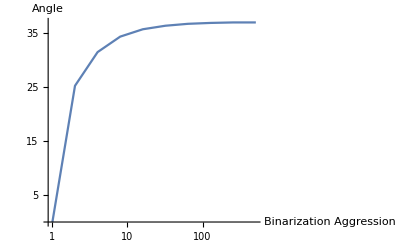

```mathematica
SeedRandom[5];
hbActForward[x_, hBL_] :=Module[{row, col,tempMat, matCreate, joinerMat, x2}, 
x2 = Transpose[x];
For[col = 1, col ≤ Dimensions[x2][[2]], col++,matCreate = Abs[ArrayReshape[x2[[;;, col]], {Ceiling[Dimensions[x2][[1]]/hBL],hBL}, 0]];
tempMat = Map[Mean, matCreate[[;;-2, ;;]], {1}];
If[Mod[Dimensions[x2][[1]], hBL]≠ 0,
AppendTo[tempMat, Total[matCreate[[-1, ;;]]]/Mod[Dimensions[x2][[1]], hBL]],
AppendTo[tempMat, Mean[matCreate[[-1, ;;]]]]];
For[row = 1, row ≤ Dimensions[x2][[1]], row++,
x2[[row, col]] = Sign[x2[[row, col]]]*tempMat[[Ceiling[row/hBL]]];
];
];
Return[Transpose[x2]]];
matrix = RandomVariate[NormalDistribution[], {256, 256}];
f[x_] :=  VectorAngle[Flatten@matrix, Flatten@hbWForward[matrix, x]]/Degree;
ListLinePlot[Transpose[{2^(Range@10 - 1), Map[f, 2^(Range@10 - 1)]}], ScalingFunctions->{"Log", "Linear"}, AxesLabel->{"Binarization Aggression", "Angle"}]
```

```mathematica
vectorHBNN//Dimensions
```

{256}

```mathematica
2^Range@5
```

{2,4,8,16,32}

```mathematica
MatrixForm@x
```

(-1.23641 | 0.617393 | 0.461547 | -0.378658 | 0.398499 | -0.401769 | -0.0616883 | 0.61485
1.0848 | 1.28933 | 0.578467 | -0.441732 | -0.436387 | 1.4804 | -0.498808 | 0.91676
-0.747106 | -0.567444 | -0.0430138 | 0.0988341 | -1.7733 | 0.0383258 | 0.295998 | -1.08018
0.87561 | -1.95597 | -1.18459 | -1.1717 | 0.732696 | 0.645561 | 1.11563 | 0.318986
0.36372 | 0.293922 | 0.633655 | -0.51749 | 2.52925 | -0.192291 | -1.39094 | 1.16483
-2.00702 | -0.530408 | 0.00658334 | -3.16668 | 0.319288 | -0.825423 | 0.231274 | -0.349782
-0.270571 | 0.84175 | -0.373648 | -0.511643 | -0.663975 | -0.448991 | -1.38002 | 0.136271
0.571544 | 1.4964 | 0.0563582 | 1.49521 | 0.534349 | -0.135581 | -2.34474 | 1.02434)

```mathematica
MatrixForm@hbWForward[x, 4]
```

(-0.690436 | 0.833145 | -1.5384 | -0.817725 | 0.643826 | 1.04678 | -0.749008 | 0.392093
-0.690436 | -0.833145 | -1.5384 | 0.817725 | 0.643826 | 1.04678 | 0.749008 | 0.392093
0.690436 | -0.833145 | 1.5384 | 0.817725 | -0.643826 | 1.04678 | -0.749008 | -0.392093
-0.690436 | 0.833145 | -1.5384 | -0.817725 | 0.643826 | 1.04678 | 0.749008 | 0.392093
-0.614427 | -0.733339 | 1.16373 | -0.58786 | -0.917065 | -1.58346 | 0.895653 | -0.716967
0.614427 | -0.733339 | 1.16373 | 0.58786 | -0.917065 | -1.58346 | 0.895653 | 0.716967
0.614427 | -0.733339 | 1.16373 | 0.58786 | 0.917065 | 1.58346 | -0.895653 | 0.716967
-0.614427 | 0.733339 | 1.16373 | -0.58786 | 0.917065 | 1.58346 | -0.895653 | -0.716967)